## Thermodynamic quantities: Condensate Ansatz

## Calculations related to evaluation of Ω:

```mathematica
Clear[t,u,c1,c2]
```

```mathematica
Clear[u]
```

```mathematica
JacobiSN[-I a ,-1]
```

-JacobiSN[ⅈ a,-1]

```mathematica
u[t_]=c1 JacobiSN[c1(-I t+c2),-1]
```

c1 JacobiSN[c1 (c2-ⅈ t),-1]

```mathematica
6 D[u[t],t]^2+6 u[t]^4//Simplify
```

6 c1^4 (-JacobiCN[c1 (c2-ⅈ t),-1]^2 JacobiDN[c1 (c2-ⅈ t),-1]^2+JacobiSN[c1 (c2-ⅈ t),-1]^4)

```mathematica
-JacobiCN[c1 (c2-ⅈ t),-1]^2 JacobiDN[c1 (c2-ⅈ t),-1]^2+JacobiSN[c1 (c2-ⅈ t),-1]^4//FullSimplify
```

-1+2 JacobiSN[c1 (c2-ⅈ t),-1]^4

```mathematica
Integrate[-1+2 JacobiSN[c1 (c2-ⅈ t),-1]^4,t]
```

-t+(2 ⅈ (c1 (c2-ⅈ t)-JacobiCN[c1 (c2-ⅈ t),-1] JacobiDN[c1 (c2-ⅈ t),-1] JacobiSN[c1 (c2-ⅈ t),-1]))/(3 c1)

```mathematica
D[-t+(2 ⅈ (c1 (c2-ⅈ t)-JacobiCN[c1 (c2-ⅈ t),-1] JacobiDN[c1 (c2-ⅈ t),-1] JacobiSN[c1 (c2-ⅈ t),-1]))/(3 c1),t]
```

-1+1/(3 c1)2 ⅈ (-ⅈ c1+ⅈ c1 JacobiCN[c1 (c2-ⅈ t),-1]^2 JacobiDN[c1 (c2-ⅈ t),-1]^2+ⅈ c1 JacobiCN[c1 (c2-ⅈ t),-1]^2 JacobiSN[c1 (c2-ⅈ t),-1]^2-ⅈ c1 JacobiDN[c1 (c2-ⅈ t),-1]^2 JacobiSN[c1 (c2-ⅈ t),-1]^2)

```mathematica
%//FullSimplify
```

-1+2 JacobiSN[c1 (c2-ⅈ t),-1]^4

```mathematica
D[JacobiCN[c1 (c2-ⅈ t),-1] JacobiDN[c1 (c2-ⅈ t),-1] JacobiSN[c1 (c2-ⅈ t),-1],t]
```

-ⅈ c1 JacobiCN[c1 (c2-ⅈ t),-1]^2 JacobiDN[c1 (c2-ⅈ t),-1]^2-ⅈ c1 JacobiCN[c1 (c2-ⅈ t),-1]^2 JacobiSN[c1 (c2-ⅈ t),-1]^2+ⅈ c1 JacobiDN[c1 (c2-ⅈ t),-1]^2 JacobiSN[c1 (c2-ⅈ t),-1]^2

```mathematica
%//FullSimplify
```

ⅈ c1 (-1+3 JacobiSN[c1 (c2-ⅈ t),-1]^4)

```mathematica
Integrate[-1+2 JacobiSN[4I EllipticK[-1]T(c2-ⅈ t),-1]^4,{t,0,1/T}]
```

-1/(3 T)

```mathematica
Integrate[6 c1^4 (-JacobiCN[c1 (c2-ⅈ t),-1]^2 JacobiDN[c1 (c2-ⅈ t),-1]^2+JacobiSN[c1 (c2-ⅈ t),-1]^4),{t,0,β}]
```

-2 c1^3 (c1 β-2 ⅈ JacobiCN[c1 c2,-1] JacobiDN[c1 c2,-1] JacobiSN[c1 c2,-1]+2 ⅈ JacobiCN[c1 (c2-ⅈ β),-1] JacobiDN[c1 (c2-ⅈ β),-1] JacobiSN[c1 (c2-ⅈ β),-1])

```mathematica
3 D[u[t],t]^2//Simplify
```

-3 c1^4 JacobiCN[c1 (c2-ⅈ t),-1]^2 JacobiDN[c1 (c2-ⅈ t),-1]^2

```mathematica
Integrate[-3 c1^4 JacobiCN[c1 (c2-ⅈ t),-1]^2 JacobiDN[c1 (c2-ⅈ t),-1]^2,{t,0,β}]
```

-c1^3 (2 c1 β-ⅈ JacobiCN[c1 c2,-1] JacobiDN[c1 c2,-1] JacobiSN[c1 c2,-1]+ⅈ JacobiCN[c1 (c2-ⅈ β),-1] JacobiDN[c1 (c2-ⅈ β),-1] JacobiSN[c1 (c2-ⅈ β),-1])

```mathematica
Clear[c1]
```

```mathematica
6 c1^4 (-JacobiCN[c1 (c2-ⅈ t),-1]^2 JacobiDN[c1 (c2-ⅈ t),-1]^2+JacobiSN[c1 (c2-ⅈ t),-1]^4)//FullSimplify
```

6 c1^4 (-1+2 JacobiSN[c1 (c2-ⅈ t),-1]^4)

```mathematica
Integrate[6 c1^4 (-1+2 JacobiSN[4EllipticK[-1] t/(2π),-1]^4),{t,0,2π}]
```

-4 c1^4 π

## Thermodynamic potential and other Thermodynamic quantities

```mathematica
Clear[Nf,μ,β,c1,c2,g,Nc,β0]
```

```mathematica
Ω[T_]=-π^2/45 T^4 (Nc^2-1)-7 π^2/180 T^4 Nc Nf -(-1/(4 g^2)+1/2 β0 Log[μ/(4π T)]-1/(4π)^2 Nf/3 Log[4])2 c1^3(c1 -2 ⅈ T JacobiCN[c1 c2,-1] JacobiDN[c1 c2,-1] JacobiSN[c1 c2,-1]+2 ⅈ T JacobiCN[c1 (c2-ⅈ/T),-1] JacobiDN[c1 (c2-ⅈ/T),-1] JacobiSN[c1 (c2-ⅈ/T),-1])-1/3 1/(4π)^2(Nf-Nc)c1^3(2c1- I T JacobiCN[c1 c2,-1]JacobiSN[c1 c2,-1]JacobiDN[c1 c2,-1]+ I T JacobiCN[c1 (c2-I/T),-1]JacobiSN[c1 (c2-I/T),-1]JacobiDN[c1 (c2-I/T),-1]);
```

Pressure

```mathematica
P[T_]=-Ω[T];
```

```mathematica
P[T]
```

1/45 (-1+Nc^2) π^2 T^4+7/180 Nc Nf π^2 T^4+(c1^3 (-Nc+Nf) (2 c1-ⅈ T JacobiCN[c1 c2,-1] JacobiDN[c1 c2,-1] JacobiSN[c1 c2,-1]+ⅈ T JacobiCN[c1 (c2-ⅈ/T),-1] JacobiDN[c1 (c2-ⅈ/T),-1] JacobiSN[c1 (c2-ⅈ/T),-1]))/(48 π^2)+2 c1^3 (c1-2 ⅈ T JacobiCN[c1 c2,-1] JacobiDN[c1 c2,-1] JacobiSN[c1 c2,-1]+2 ⅈ T JacobiCN[c1 (c2-ⅈ/T),-1] JacobiDN[c1 (c2-ⅈ/T),-1] JacobiSN[c1 (c2-ⅈ/T),-1]) (-1/(4 g^2)-(Nf Log[4])/(48 π^2)+1/2 β0 Log[μ/(4 π T)])

Entropy Density

```mathematica
s[T_]=-D[Ω[T],T];
```

```mathematica
s[T]
```

4/45 (-1+Nc^2) π^2 T^3+7/45 Nc Nf π^2 T^3-(c1^3 β0 (c1-2 ⅈ T JacobiCN[c1 c2,-1] JacobiDN[c1 c2,-1] JacobiSN[c1 c2,-1]+2 ⅈ T JacobiCN[c1 (c2-ⅈ/T),-1] JacobiDN[c1 (c2-ⅈ/T),-1] JacobiSN[c1 (c2-ⅈ/T),-1]))/T+1/(48 π^2)c1^3 (-Nc+Nf) (-(c1 JacobiCN[c1 (c2-ⅈ/T),-1]^2 JacobiDN[c1 (c2-ⅈ/T),-1]^2)/T-ⅈ JacobiCN[c1 c2,-1] JacobiDN[c1 c2,-1] JacobiSN[c1 c2,-1]+ⅈ JacobiCN[c1 (c2-ⅈ/T),-1] JacobiDN[c1 (c2-ⅈ/T),-1] JacobiSN[c1 (c2-ⅈ/T),-1]-(c1 JacobiCN[c1 (c2-ⅈ/T),-1]^2 JacobiSN[c1 (c2-ⅈ/T),-1]^2)/T+(c1 JacobiDN[c1 (c2-ⅈ/T),-1]^2 JacobiSN[c1 (c2-ⅈ/T),-1]^2)/T)+2 c1^3 (-(2 c1 JacobiCN[c1 (c2-ⅈ/T),-1]^2 JacobiDN[c1 (c2-ⅈ/T),-1]^2)/T-2 ⅈ JacobiCN[c1 c2,-1] JacobiDN[c1 c2,-1] JacobiSN[c1 c2,-1]+2 ⅈ JacobiCN[c1 (c2-ⅈ/T),-1] JacobiDN[c1 (c2-ⅈ/T),-1] JacobiSN[c1 (c2-ⅈ/T),-1]-(2 c1 JacobiCN[c1 (c2-ⅈ/T),-1]^2 JacobiSN[c1 (c2-ⅈ/T),-1]^2)/T+(2 c1 JacobiDN[c1 (c2-ⅈ/T),-1]^2 JacobiSN[c1 (c2-ⅈ/T),-1]^2)/T) (-1/(4 g^2)-(Nf Log[4])/(48 π^2)+1/2 β0 Log[μ/(4 π T)])

Energy Density

```mathematica
ϵ[T_]=-T^2 D[Ω[T]/T,T];
```

```mathematica
ϵ[T]//Simplify
```

1/240 ((120 c1^4)/g^2+(10 c1^4 Nc)/π^2-(10 c1^4 Nf)/π^2-16 π^2 T^4+16 Nc^2 π^2 T^4+28 Nc Nf π^2 T^4-240 c1^4 β0+480 ⅈ c1^3 T β0 JacobiCN[c1 c2,-1] JacobiDN[c1 c2,-1] JacobiSN[c1 c2,-1]-480 ⅈ c1^3 T β0 JacobiCN[c1 (c2-ⅈ/T),-1] JacobiDN[c1 (c2-ⅈ/T),-1] JacobiSN[c1 (c2-ⅈ/T),-1]-(240 c1^4 JacobiDN[c1 (c2-ⅈ/T),-1]^2 JacobiSN[c1 (c2-ⅈ/T),-1]^2)/g^2-(5 c1^4 Nc JacobiDN[c1 (c2-ⅈ/T),-1]^2 JacobiSN[c1 (c2-ⅈ/T),-1]^2)/π^2+(5 c1^4 Nf JacobiDN[c1 (c2-ⅈ/T),-1]^2 JacobiSN[c1 (c2-ⅈ/T),-1]^2)/π^2+(10 c1^4 Nf Log[4])/π^2-(20 c1^4 Nf JacobiDN[c1 (c2-ⅈ/T),-1]^2 JacobiSN[c1 (c2-ⅈ/T),-1]^2 Log[4])/π^2-240 c1^4 β0 Log[μ/(4 π T)]+480 c1^4 β0 JacobiDN[c1 (c2-ⅈ/T),-1]^2 JacobiSN[c1 (c2-ⅈ/T),-1]^2 Log[μ/(4 π T)]-(5 c1^4 JacobiCN[c1 (c2-ⅈ/T),-1]^2 (JacobiDN[c1 (c2-ⅈ/T),-1]^2+JacobiSN[c1 (c2-ⅈ/T),-1]^2) (-48 π^2+g^2 (-Nc+Nf-4 Nf Log[4])+96 g^2 π^2 β0 Log[μ/(4 π T)]))/(g^2 π^2))

Trace Anomaly

```mathematica
Θ[T_]=-T^5 D[Ω[T]/T^4,T];
```

```mathematica
Θ[T]//Simplify
```

1/(48 g^2 π^2)c1^3 (8 c1 (12 π^2+g^2 (Nc-6 π^2 β0+Nf (-1+Log[4]))-24 g^2 π^2 β0 Log[μ/(4 π T)])+c1 JacobiDN[c1 (c2-ⅈ/T),-1]^2 JacobiSN[c1 (c2-ⅈ/T),-1]^2 (-48 π^2+g^2 (-Nc+Nf-4 Nf Log[4])+96 g^2 π^2 β0 Log[μ/(4 π T)])-c1 JacobiCN[c1 (c2-ⅈ/T),-1]^2 (JacobiDN[c1 (c2-ⅈ/T),-1]^2+JacobiSN[c1 (c2-ⅈ/T),-1]^2) (-48 π^2+g^2 (-Nc+Nf-4 Nf Log[4])+96 g^2 π^2 β0 Log[μ/(4 π T)])+3 ⅈ T JacobiCN[c1 c2,-1] JacobiDN[c1 c2,-1] JacobiSN[c1 c2,-1] (-48 π^2+g^2 (-Nc+Nf+32 π^2 β0-4 Nf Log[4])+96 g^2 π^2 β0 Log[μ/(4 π T)])-3 ⅈ T JacobiCN[c1 (c2-ⅈ/T),-1] JacobiDN[c1 (c2-ⅈ/T),-1] JacobiSN[c1 (c2-ⅈ/T),-1] (-48 π^2+g^2 (-Nc+Nf+32 π^2 β0-4 Nf Log[4])+96 g^2 π^2 β0 Log[μ/(4 π T)]))

Specific heat

```mathematica
Subscript[C, v][T_]=(4 ϵ[T]/T^4+3 Θ[T]/T^4+T D[Θ[T]/T^4,T])T^3;
```

```mathematica
Subscript[C, v][T]//Simplify
```

1/(60 g^2 π^2 T^2)(240 c1^4 g^2 π^2 T β0 JacobiCN[c1 (c2-ⅈ/T),-1]^2 (JacobiDN[c1 (c2-ⅈ/T),-1]^2+JacobiSN[c1 (c2-ⅈ/T),-1]^2)+4 g^2 π^2 T (-4 π^2 T^4+4 Nc^2 π^2 T^4+7 Nc Nf π^2 T^4+15 c1^4 β0+30 ⅈ c1^3 T β0 JacobiCN[c1 c2,-1] JacobiDN[c1 c2,-1] JacobiSN[c1 c2,-1]-60 c1^4 β0 JacobiDN[c1 (c2-ⅈ/T),-1]^2 JacobiSN[c1 (c2-ⅈ/T),-1]^2)-5 ⅈ c1^5 JacobiCN[c1 (c2-ⅈ/T),-1]^3 JacobiDN[c1 (c2-ⅈ/T),-1] JacobiSN[c1 (c2-ⅈ/T),-1] (-48 π^2+g^2 (-Nc+Nf-4 Nf Log[4])+96 g^2 π^2 β0 Log[μ/(4 π T)])+5 ⅈ c1^3 JacobiCN[c1 (c2-ⅈ/T),-1] JacobiDN[c1 (c2-ⅈ/T),-1] JacobiSN[c1 (c2-ⅈ/T),-1] (-24 g^2 π^2 T^2 β0+c1^2 JacobiDN[c1 (c2-ⅈ/T),-1]^2 (-48 π^2+g^2 (-Nc+Nf-4 Nf Log[4])+96 g^2 π^2 β0 Log[μ/(4 π T)])+c1^2 JacobiSN[c1 (c2-ⅈ/T),-1]^2 (-48 π^2+g^2 (-Nc+Nf-4 Nf Log[4])+96 g^2 π^2 β0 Log[μ/(4 π T)])))

Speed of Sound

```mathematica
Subscript[C, s][T_]=s[T]/(Subscript[C, v][T]);
```

```mathematica
Subscript[C, s][T]//Simplify
```

(T (-64 g^2 π^4 T^4+64 g^2 Nc^2 π^4 T^4+112 g^2 Nc Nf π^4 T^4-720 c1^4 g^2 π^2 β0-15 c1^4 g^2 Nc JacobiDN[c1 (c2-ⅈ/T),-1]^2 JacobiSN[c1 (c2-ⅈ/T),-1]^2+15 c1^4 g^2 Nf JacobiDN[c1 (c2-ⅈ/T),-1]^2 JacobiSN[c1 (c2-ⅈ/T),-1]^2-720 c1^4 π^2 JacobiDN[c1 (c2-ⅈ/T),-1]^2 JacobiSN[c1 (c2-ⅈ/T),-1]^2-60 c1^4 g^2 Nf JacobiDN[c1 (c2-ⅈ/T),-1]^2 JacobiSN[c1 (c2-ⅈ/T),-1]^2 Log[4]+1440 c1^4 g^2 π^2 β0 JacobiDN[c1 (c2-ⅈ/T),-1]^2 JacobiSN[c1 (c2-ⅈ/T),-1]^2 Log[μ/(4 π T)]-15 c1^4 JacobiCN[c1 (c2-ⅈ/T),-1]^2 (JacobiDN[c1 (c2-ⅈ/T),-1]^2+JacobiSN[c1 (c2-ⅈ/T),-1]^2) (-48 π^2+g^2 (-Nc+Nf-4 Nf Log[4])+96 g^2 π^2 β0 Log[μ/(4 π T)])-15 ⅈ c1^3 T JacobiCN[c1 c2,-1] JacobiDN[c1 c2,-1] JacobiSN[c1 c2,-1] (-48 π^2-g^2 (Nc-Nf+96 π^2 β0+4 Nf Log[4])+96 g^2 π^2 β0 Log[μ/(4 π T)])+15 ⅈ c1^3 T JacobiCN[c1 (c2-ⅈ/T),-1] JacobiDN[c1 (c2-ⅈ/T),-1] JacobiSN[c1 (c2-ⅈ/T),-1] (-48 π^2-g^2 (Nc-Nf+96 π^2 β0+4 Nf Log[4])+96 g^2 π^2 β0 Log[μ/(4 π T)])))/(12 (240 c1^4 g^2 π^2 T β0 JacobiCN[c1 (c2-ⅈ/T),-1]^2 (JacobiDN[c1 (c2-ⅈ/T),-1]^2+JacobiSN[c1 (c2-ⅈ/T),-1]^2)+4 g^2 π^2 T (-4 π^2 T^4+4 Nc^2 π^2 T^4+7 Nc Nf π^2 T^4+15 c1^4 β0+30 ⅈ c1^3 T β0 JacobiCN[c1 c2,-1] JacobiDN[c1 c2,-1] JacobiSN[c1 c2,-1]-60 c1^4 β0 JacobiDN[c1 (c2-ⅈ/T),-1]^2 JacobiSN[c1 (c2-ⅈ/T),-1]^2)-5 ⅈ c1^5 JacobiCN[c1 (c2-ⅈ/T),-1]^3 JacobiDN[c1 (c2-ⅈ/T),-1] JacobiSN[c1 (c2-ⅈ/T),-1] (-48 π^2+g^2 (-Nc+Nf-4 Nf Log[4])+96 g^2 π^2 β0 Log[μ/(4 π T)])+5 ⅈ c1^3 JacobiCN[c1 (c2-ⅈ/T),-1] JacobiDN[c1 (c2-ⅈ/T),-1] JacobiSN[c1 (c2-ⅈ/T),-1] (-24 g^2 π^2 T^2 β0+c1^2 JacobiDN[c1 (c2-ⅈ/T),-1]^2 (-48 π^2+g^2 (-Nc+Nf-4 Nf Log[4])+96 g^2 π^2 β0 Log[μ/(4 π T)])+c1^2 JacobiSN[c1 (c2-ⅈ/T),-1]^2 (-48 π^2+g^2 (-Nc+Nf-4 Nf Log[4])+96 g^2 π^2 β0 Log[μ/(4 π T)]))))

## Ideal Gas limits

```mathematica
Clear[Pideal,Sideal,Eideal]
```

```mathematica
Nc=2;Nf=2;
Pideal[T_]=π^2/45 T^4(Nc^2-1)+(7 π^2)/180 T^4 Nc Nf;
Eideal[T_]=π^2/15 T^4(Nc^2-1)+(7 π^2)/60 T^4 Nc Nf;
Sideal[T_]=4 π^2/45 T^3(Nc^2-1+7/4 Nc Nf);
```

```mathematica
Pideal[T]
```

(2 π^2 T^4)/9

```mathematica
Eideal
```

(19 π^2 T^4)/12

```mathematica
Sideal
```

(19 π^2 T^3)/9

```mathematica
91200/Exp[(6π)/(23(0.1184))]//N
```

89.9244

## Lattice results SU(3)

```mathematica
Pr={0.34,0.38,0.42,0.47,0.52,0.6,0.68,0.77,0.87,0.97,1.08,1.19,1.30,1.40,1.61,1.98,2.29,2.55,2.77,2.95,3.10,3.24,3.35,3.44,3.52}
```

{0.34,0.38,0.42,0.47,0.52,0.6,0.68,0.77,0.87,0.97,1.08,1.19,1.3,1.4,1.61,1.98,2.29,2.55,2.77,2.95,3.1,3.24,3.35,3.44,3.52}

```mathematica
te={125,130,135,140,145,150,155,160,165,170,175,180,185,190,200,220,240,260,280,300,320,340,360,380,400}
```

{125,130,135,140,145,150,155,160,165,170,175,180,185,190,200,220,240,260,280,300,320,340,360,380,400}

```mathematica
La=Table[{te[[i]],(36 Pr[[i]])/(19 π^2)},{i,1,25}]
```

{{125,0.0652722},{130,0.0729513},{135,0.0806303},{140,0.0902292},{145,0.099828},{150,0.115186},{155,0.130544},{160,0.147822},{165,0.16702},{170,0.186218},{175,0.207335},{180,0.228453},{185,0.24957},{190,0.268768},{200,0.309083},{220,0.380114},{240,0.439627},{260,0.489541},{280,0.531776},{300,0.566332},{320,0.595129},{340,0.622005},{360,0.643123},{380,0.660401},{400,0.675759}}

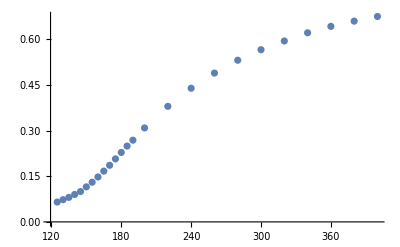

```mathematica
p2=ListPlot[La]
```

```mathematica
(*Hot QCD collabration*)
```

```mathematica
Pvalues={0.439,0.481,0.529,0.586,0.651,0.726,0.808,0.898,0.994,1.094,1.197,1.302,1.406,1.510,1.613,1.713,1.810,1.904,1.995,2.083,2.168,2.249,2.328,2.403,2.476,2.546,2.613,2.678,2.741,2.801,2.859,2.915,2.969,3.021,3.072,3.120,3.167,3.212,3.256,3.298,3.338,3.377,3.415,3.452,3.487,3.521,3.554,3.586,3.617,3.647,3.675,3.703,3.730,3.756,3.782}
```

{0.439,0.481,0.529,0.586,0.651,0.726,0.808,0.898,0.994,1.094,1.197,1.302,1.406,1.51,1.613,1.713,1.81,1.904,1.995,2.083,2.168,2.249,2.328,2.403,2.476,2.546,2.613,2.678,2.741,2.801,2.859,2.915,2.969,3.021,3.072,3.12,3.167,3.212,3.256,3.298,3.338,3.377,3.415,3.452,3.487,3.521,3.554,3.586,3.617,3.647,3.675,3.703,3.73,3.756,3.782}

```mathematica
temp=Table[130+5x,{x,0,54}]
```

{130,135,140,145,150,155,160,165,170,175,180,185,190,195,200,205,210,215,220,225,230,235,240,245,250,255,260,265,270,275,280,285,290,295,300,305,310,315,320,325,330,335,340,345,350,355,360,365,370,375,380,385,390,395,400}

```mathematica
LatticehotQCD=Table[{temp[[i]],(36 Pvalues[[i]])/(19 π^2)},{i,1,55}]
```

{{130,0.0842779},{135,0.0923409},{140,0.101556},{145,0.112499},{150,0.124977},{155,0.139375},{160,0.155117},{165,0.172395},{170,0.190825},{175,0.210023},{180,0.229796},{185,0.249954},{190,0.26992},{195,0.289885},{200,0.309659},{205,0.328857},{210,0.347478},{215,0.365524},{220,0.382994},{225,0.399888},{230,0.416206},{235,0.431756},{240,0.446922},{245,0.461321},{250,0.475335},{255,0.488773},{260,0.501636},{265,0.514114},{270,0.526209},{275,0.537728},{280,0.548862},{285,0.559613},{290,0.56998},{295,0.579962},{300,0.589753},{305,0.598968},{310,0.607991},{315,0.61663},{320,0.625077},{325,0.63314},{330,0.640819},{335,0.648306},{340,0.655601},{345,0.662705},{350,0.669424},{355,0.675951},{360,0.682286},{365,0.688429},{370,0.694381},{375,0.70014},{380,0.705515},{385,0.710891},{390,0.716074},{395,0.721066},{400,0.726057}}

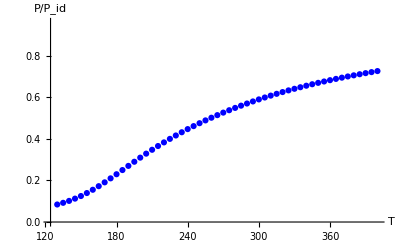

```mathematica
plattice=ListPlot[LatticehotQCD,AxesLabel->{"T","P/P_id"},PlotStyle->Blue,PlotRange->{0,0.96}]
```

## Normalised Plots

Replace g with 4π αs[T] for plotting

```mathematica
Λms=200;
```

```mathematica
Clear[c1,c2,Λ,β0,T,Λms]
Λ=π T;β0=1/(4π)^2(11/3 Nc-2/3 Nf);
α[T_,Λms_]=2Log[Λ/Λms];
αs[T_,Λms_]=1/(4π β0 α[T,Λms])(1);(*For only loop *)
Press[c1_,c2_,T_,Λms_]= -(-1/45 (-1+Nc^2) π^2 (T)^4-7/180 Nc Nf π^2 (T)^4-1/(48 π^2)c1^3 (-Nc+Nf) (2 c1-ⅈ T JacobiCN[c1 c2,-1] JacobiDN[c1 c2,-1] JacobiSN[c1 c2,-1]+ⅈ T JacobiCN[c1 (c2-ⅈ/T),-1] JacobiDN[c1 (c2-ⅈ/T),-1] JacobiSN[c1 (c2-ⅈ/T),-1])-2 c1^3 (c1-2 ⅈ T JacobiCN[c1 c2,-1] JacobiDN[c1 c2,-1] JacobiSN[c1 c2,-1]+2 ⅈ T JacobiCN[c1 (c2-ⅈ/T),-1] JacobiDN[c1 (c2-ⅈ/T),-1] JacobiSN[c1 (c2-ⅈ/T),-1]) (-(1/(4 (4π) αs[T,Λms]))-(Nf Log[4])/(48 π^2)+1/2 β0 Log[Λ/(4 π T)]));
Thdpot[c1_,c2_,T_,Λms_]= (-1/45 (-1+Nc^2) π^2 (T)^4-7/180 Nc Nf π^2 (T)^4-1/(48 π^2)c1^3 (-Nc+Nf) (2 c1-ⅈ T JacobiCN[c1 c2,-1] JacobiDN[c1 c2,-1] JacobiSN[c1 c2,-1]+ⅈ T JacobiCN[c1 (c2-ⅈ/T),-1] JacobiDN[c1 (c2-ⅈ/T),-1] JacobiSN[c1 (c2-ⅈ/T),-1])-2 c1^3 (c1-2 ⅈ T JacobiCN[c1 c2,-1] JacobiDN[c1 c2,-1] JacobiSN[c1 c2,-1]+2 ⅈ T JacobiCN[c1 (c2-ⅈ/T),-1] JacobiDN[c1 (c2-ⅈ/T),-1] JacobiSN[c1 (c2-ⅈ/T),-1]) (-(1/(4 (4π) αs[T,Λms]))-(Nf Log[4])/(48 π^2)+1/2 β0 Log[Λ/(4 π T)]));
```

```mathematica
Sden[c1_,c2_,T_,Λms_]=-D[Thdpot[c1,c2,T,Λms],T];
```

```mathematica
Enden[c1_,c2_,T_,Λms_]= -Press[c1,c2,T,Λms]+ T Sden[c1,c2,T,Λms];
```

```mathematica
Press1[c1_,c2_,T_,Λms_]=Press[c1,c2,T,Λms]/Pideal[T];
Thdpot1[c1_,c2_,T_,Λms_]=Thdpot[c1,c2,T,Λms]/Pideal[T];
Sden1[c1_,c2_,T_,Λms_]=Sden[c1,c2,T,Λms]/Sideal[T];
Enden1[c1_,c2_,T_,Λms_]=Enden[c1,c2,T,Λms]/Eideal[T];
```

### Case A: Condensate is not in equilibrium with quantum fluctuations

```mathematica
(*For c2=0 and for c2 << β *)
```

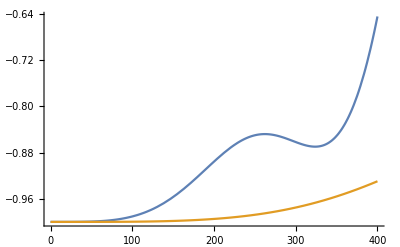

```mathematica
Plot[{Thdpot1[c1,0,200],Thdpot1[c1,0,500]},{c1,0,400}]
```

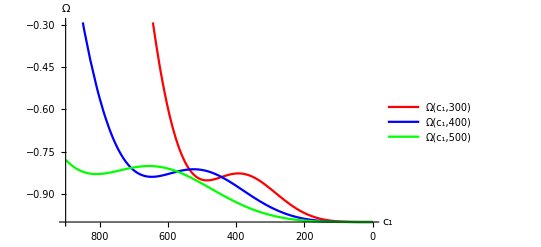

```mathematica
Plot[{Thdpot1[c1,0,300],Thdpot1[c1,0,400],Thdpot1[c1,0,500]},{c1,900,0},AxesOrigin->{900,-1},PlotStyle->{Red,Blue,Green},AxesLabel->{"c_1","Ω"},PlotLegends->Placed[{"Ω(c_1,300)","Ω(c_1,400)","Ω(c_1,500)"},{Scaled[{0.5,0.9}], {0, 0.8}}],ScalingFunctions->{"Reverse",Automatic}]
```

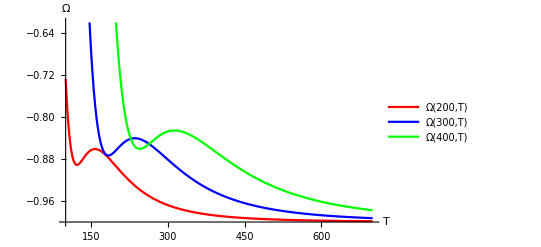

```mathematica
Plot[{Thdpot1[200,0,T],Thdpot1[300,0,T],Thdpot1[400,0,T]},{T,100,700},AxesOrigin->{100,-1},PlotStyle->{Red,Blue,Green},AxesLabel->{"T","Ω"},PlotLegends->Placed[{"Ω(200,T)","Ω(300,T)","Ω(400,T)"},{Right,Center}]]
```

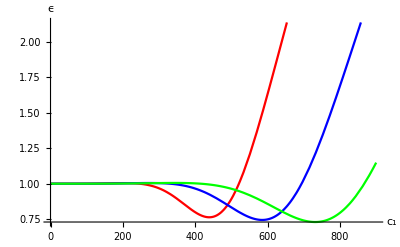

```mathematica
Plot[{Enden1[c1,0,300],Enden1[c1,0,400],Enden1[c1,0,500]},{c1,900,0},PlotStyle->{Red,Blue,Green},AxesLabel->{"c_1","ϵ"}]
```

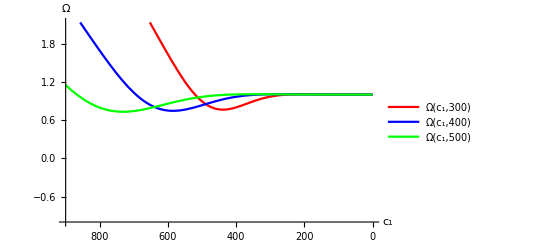

```mathematica
Plot[{Enden1[c1,0,300],Enden1[c1,0,400],Enden1[c1,0,500]},{c1,900,0},AxesOrigin->{900,-1},PlotStyle->{Red,Blue,Green},AxesLabel->{"c_1","Ω"},PlotLegends->Placed[{"Ω(c_1,300)","Ω(c_1,400)","Ω(c_1,500)"},{Scaled[{0.5,0.9}], {0, 0.8}}],ScalingFunctions->{"Reverse",Automatic}]
```

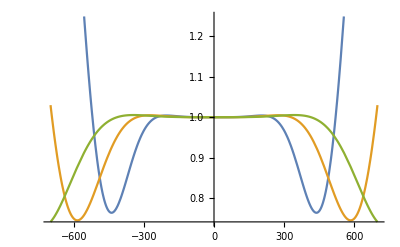

```mathematica
Plot[{Enden1[c1,0,300],Enden1[c1,0,400],Enden1[c1,0,500]},{c1,-700,700}]
```

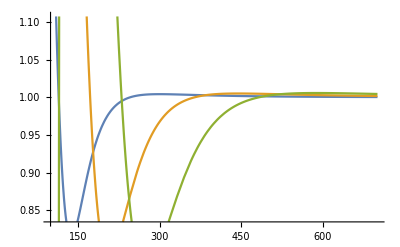

```mathematica
Plot[{Enden1[200,0,T],Enden1[300,0,T],Enden1[400,0,T]},{T,100,700}]
```

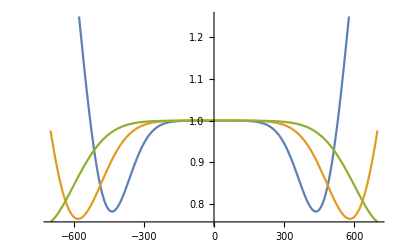

```mathematica
Plot[{Sden1[c1,0,300],Sden1[c1,0,400],Sden1[c1,0,500]},{c1,-700,700}]
```

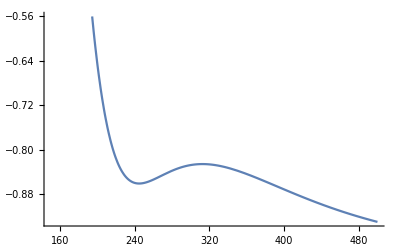

```mathematica
Plot[Thdpot1[400,0,T],{T,150,500}]
```

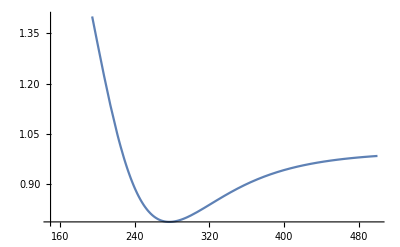

```mathematica
Plot[Sden1[400,0,T],{T,150,500}]
```

```mathematica
(*For c2 \neq 0*)
```

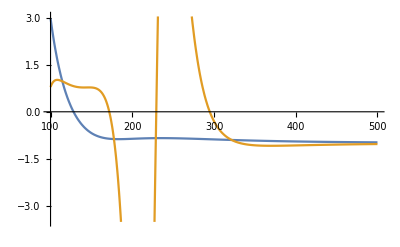

```mathematica
Plot[{Thdpot1[300,0,T],Re[Thdpot1[300,1,T]]},{T,100,500}]
```

```mathematica
Table[Thdpot1[300,c2,300],{c2,0,10,0.5}]
```

{-0.881468+0. ⅈ,-0.744993-0.125965 ⅈ,-0.302571+1.91826 ⅈ,0.0353981-0.861352 ⅈ,-0.799456+0.10913 ⅈ,-0.878948-0.0218379 ⅈ,-0.66153-0.129674 ⅈ,-1.9656+2.79818 ⅈ,-0.133509-0.260977 ⅈ,-0.834916+0.0876224 ⅈ,-0.871009-0.0439839 ⅈ,-0.534761-0.100488 ⅈ,-4.40205+1.48805 ⅈ,-0.365179+0.00500471 ⅈ,-0.857731+0.0649428 ⅈ,-0.856431-0.0665611 ⅈ,-0.349987+0.00688936 ⅈ,-4.27307-1.68171 ⅈ,-0.545567+0.104398 ⅈ,-0.871774+0.0423926 ⅈ,-0.832868-0.0892172 ⅈ}

### Case B: Condensate is in equilibrium with quantum fluctuations

```mathematica
Pideal/Eideal
```

1/3

All thermodynamics are only a function of Temperature.

```mathematica
(* c1 -> 4 I EllipticK[-1] T *)
```

```mathematica
Sden2[T_,c2_,Λms_]=-D[Thdpot[4 I EllipticK[-1] T ,c2,T,Λms],T];
```

```mathematica
Sden22[T_,c2_,Λms_]=Sden2[T,c2,Λms]/Sideal[T];
```

```mathematica
Enden2[T_,c2_,Λms_]= -Press[4I EllipticK[-1] T,c2,T,Λms]+ T Sden2[T,c2,Λms];
```

```mathematica
Enden22[T_,c2_,Λms_]=Enden2[T,c2,Λms]/Eideal[T];
```

```mathematica
Spheat2[T_,c2_,Λms_]=D[Enden2[T,c2,Λms],T];
```

```mathematica
Spheat22[T_,c2_,Λms_]=Spheat2[T,c2,Λms]/T^3;
```

```mathematica
Soundspd2[T_,c2_,Λms_]=Sden2[T,c2,Λms]/Spheat2[T,c2,Λms];
```

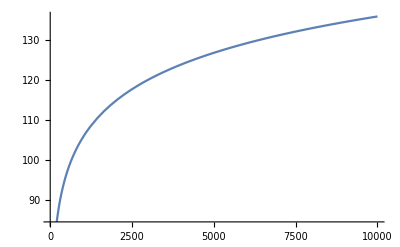

```mathematica
Plot[Thdpot1[4I EllipticK[-1] T,0,T,5],{T,10,10000}]
```

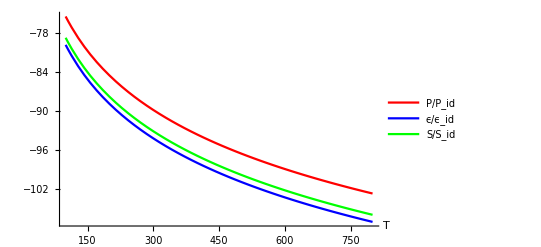

```mathematica
Plot[{Press1[4I EllipticK[-1] T,0,T,5],Enden22[T,0,5],Sden22[T,0,5]},{T,100,800},AxesLabel->{"T"},PlotStyle->{Red,Blue,Green},PlotLegends->Placed[{"P/P_id","ϵ/ϵ_id","S/S_id"},{Right,Center}]]
```

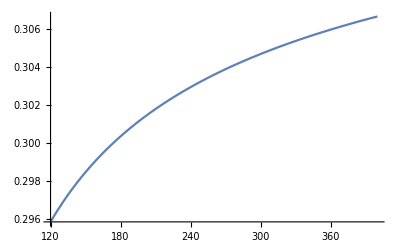

```mathematica
Plot[Soundspd2[T,0,176],{T,120,400}]
```

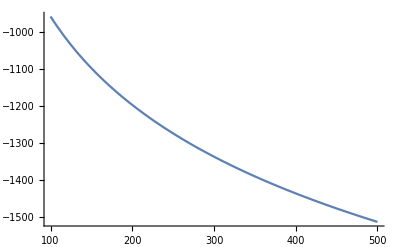

```mathematica
Plot[Spheat22[T,0,176],{T,100,500}]
```

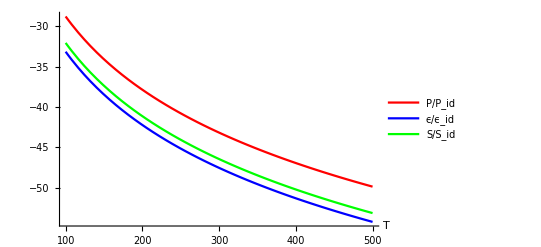

```mathematica
Plot[{Press1[4I EllipticK[-1] T,0,T,176],Enden22[T,0,176],Sden22[T,0,176]},{T,100,500},AxesLabel->{"T"},PlotStyle->{Red,Blue,Green},PlotLegends->Placed[{"P/P_id","ϵ/ϵ_id","S/S_id"},{Right,Center}]]
```

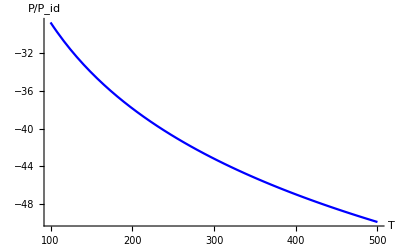

```mathematica
Plot[Press1[4I EllipticK[-1] T,0,T,176],{T,100,500},PlotStyle->Blue,AxesLabel->{"T","P/P_id"}]
```

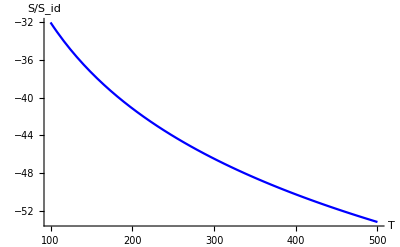

```mathematica
Plot[Sden22[T,0,176],{T,100,500},PlotStyle->Blue,AxesLabel->{"T","S/S_id"}]
```

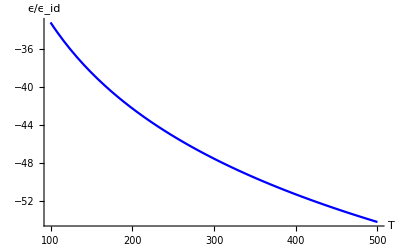

```mathematica
Plot[Enden22[T,0,176],{T,100,500},PlotStyle->Blue,AxesLabel->{"T","ϵ/ϵ_id"}]
```

```mathematica
4 EllipticK[-1]//N
```

5.24412

### HTL perturbation theory plots (Free energy) (for comparison only)

```mathematica
Λms=176;Λ=2 π T;
```

```mathematica
Clear[Λ];
α1[Λ_]=2Log[2π *1.03Λ];
αs1[Λ_]=(4π)/(11*t[Λ])(1-102/121 Log[t[Λ]]/t[Λ]);
Fn[Λ_]=1-15/(4π)αs[Λ]+30/π^(3/2)αs[Λ]^(3/2)+135/2(Log[αs[Λ]/π]+3.51)1/π^2 αs[Λ]^2-799.2/π^(5/2)αs[Λ]^(5/2) ;
```

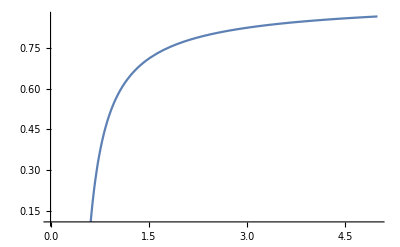

```mathematica
Plot[Fn[T],{T,0,5}]
```

## Thermodynamic quantities: Condensate Ansatz + GW

## Case A: Not in equilibrium

```mathematica
Clear[c1,c2,Ap,ωg,t,u,hp]
```

```mathematica
u[t_]=c1 JacobiSN[c1(-I t+c2),-1]
```

c1 JacobiSN[c1 (c2-ⅈ t),-1]

```mathematica
hp[t_]=Ap Cos[ ωg (-I t)]
```

Ap Cosh[t ωg]

```mathematica
(*F^2 term*)
```

```mathematica
6 D[u[t],t]^2 +6 u[t]^4+1/8 hp[t]^4 u[t]^4+hp[t]^2 D[u[t],t]^2+2 hp[t]u[t]u'[t]hp'[t]+u[t]^2 hp'[t]^2
```

-6 c1^4 JacobiCN[c1 (c2-ⅈ t),-1]^2 JacobiDN[c1 (c2-ⅈ t),-1]^2-Ap^2 c1^4 Cosh[t ωg]^2 JacobiCN[c1 (c2-ⅈ t),-1]^2 JacobiDN[c1 (c2-ⅈ t),-1]^2+6 c1^4 JacobiSN[c1 (c2-ⅈ t),-1]^4+1/8 Ap^4 c1^4 Cosh[t ωg]^4 JacobiSN[c1 (c2-ⅈ t),-1]^4-2 ⅈ Ap^2 c1^3 ωg Cosh[t ωg] JacobiCN[c1 (c2-ⅈ t),-1] JacobiDN[c1 (c2-ⅈ t),-1] JacobiSN[c1 (c2-ⅈ t),-1] Sinh[t ωg]+Ap^2 c1^2 ωg^2 JacobiSN[c1 (c2-ⅈ t),-1]^2 Sinh[t ωg]^2

```mathematica
Clear[I1,I2]
```

```mathematica
I1[T_?NumberQ]:=NIntegrate[-6 c1^4 JacobiCN[c1 (c2-ⅈ t),-1]^2 JacobiDN[c1 (c2-ⅈ t),-1]^2-Ap^2 c1^4 Cosh[t ωg]^2 JacobiCN[c1 (c2-ⅈ t),-1]^2 JacobiDN[c1 (c2-ⅈ t),-1]^2+6 c1^4 JacobiSN[c1 (c2-ⅈ t),-1]^4+1/8 Ap^4 c1^4 Cosh[t ωg]^4 JacobiSN[c1 (c2-ⅈ t),-1]^4-2 ⅈ Ap^2 c1^3 ωg Cosh[t ωg] JacobiCN[c1 (c2-ⅈ t),-1] JacobiDN[c1 (c2-ⅈ t),-1] JacobiSN[c1 (c2-ⅈ t),-1] Sinh[t ωg]+Ap^2 c1^2 ωg^2 JacobiSN[c1 (c2-ⅈ t),-1]^2 Sinh[t ωg]^2,{t,0,1/T}];
```

```mathematica
(*E^2 term*)
```

```mathematica
3 D[u[t],t]^2+1/2 hp[t]^2 u'[t]^2+hp[t]u[t]u'[t]hp'[t]+1/2 u[t]^2 hp'[t]^2//Simplify
```

-1/4 c1^2 (c1^2 (12+Ap^2+Ap^2 Cosh[2 t ωg]) JacobiCN[c1 (c2-ⅈ t),-1]^2 JacobiDN[c1 (c2-ⅈ t),-1]^2-2 Ap^2 ωg^2 JacobiSN[c1 (c2-ⅈ t),-1]^2 Sinh[t ωg]^2+2 ⅈ Ap^2 c1 ωg JacobiCN[c1 (c2-ⅈ t),-1] JacobiDN[c1 (c2-ⅈ t),-1] JacobiSN[c1 (c2-ⅈ t),-1] Sinh[2 t ωg])

```mathematica
I2[T_?NumberQ]:=NIntegrate[-1/4 c1^2 (c1^2 (12+Ap^2+Ap^2 Cosh[2 t ωg]) JacobiCN[c1 (c2-ⅈ t),-1]^2 JacobiDN[c1 (c2-ⅈ t),-1]^2-2 Ap^2 ωg^2 JacobiSN[c1 (c2-ⅈ t),-1]^2 Sinh[t ωg]^2+2 ⅈ Ap^2 c1 ωg JacobiCN[c1 (c2-ⅈ t),-1] JacobiDN[c1 (c2-ⅈ t),-1] JacobiSN[c1 (c2-ⅈ t),-1] Sinh[2 t ωg]),{t,0,1/T}];
```

```mathematica
c1=300;c2=0;ωg=1;Ap=0.001;
```

```mathematica
I1[300]
```

-1.09559×10^8+0. ⅈ

Thermodynamic Potential

```mathematica
Λms=176;Λ=2 π T;β0=1/(4π)^2(11/3 Nc-2/3 Nf);
α[T_]=2Log[Λ/Λms];
αs[T_]=1/(4π β0 α[T])(1);(*For only loop *)
```

```mathematica
Thdpotgw[T_]:=-((π^2/45)T^4 (Nc^2-1)+7 (π^2/180)T^4 Nc Nf -((-1)/(4 (4π)αs[T])+(1/2)β0 Log[Λ/(4π T)]-(1/(4π)^2)(Nf/3)Log[4])I1[T]-(1/3)(1/(4π)^2)(Nf-Nc)I2[T]);
```

```mathematica
Pgw[T_]=-Thdpotgw[T];
```

```mathematica
Sdengw[T_]=-D[Thdpotgw[T],T];
```

```mathematica
Endengw[T_]= -Pgw[T]+ T Sdengw[T];
```

```mathematica
Pgwn[T_]=Pgw[T]/Pideal;
Thdpotgwn[T_]=Thdpotgw[T]/Pideal;
Sdengwn[T_]=Sdengw[T]/Sideal;
Endengwn[T_]=Endengw[T]/Eideal;
```

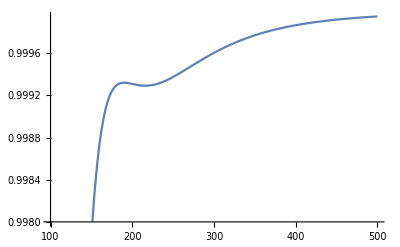

```mathematica
Plot[Re[Pgwn[T]],{T,100,500}]
```

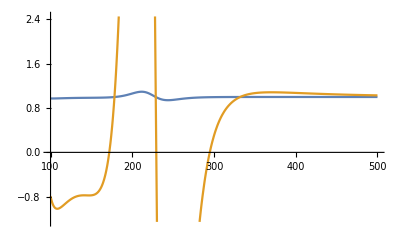

```mathematica
Plot[{Re[Pgw[T]],Re[Press1[300,1,T]]},{T,100,500}]
```

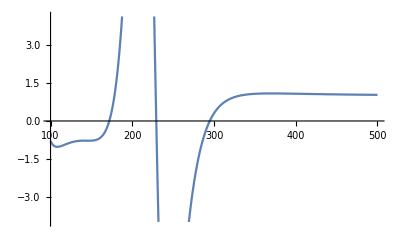

```mathematica
p2=Plot[Re[Press1[300,1,T]],{T,100,500}]
```

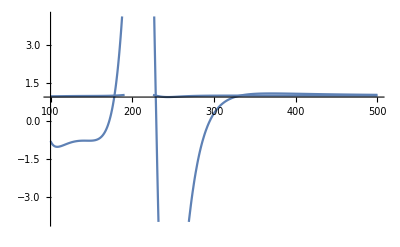

```mathematica
Show[{p1,p2},PlotRange->All]
```

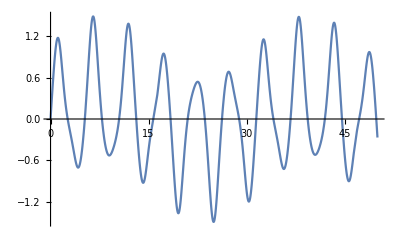

```mathematica
Plot[(1+1/2 Cos[t])JacobiSN[t,-1],{t,0,50}]
```

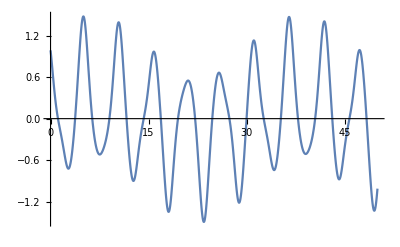

```mathematica
Plot[(1+1/2 Cos[t+2π 4EllipticK[-1]])JacobiSN[t+2π 4EllipticK[-1],-1],{t,0,50}]
```

```mathematica
4 EllipticK[-1]//N
```

5.24412

## Case B: Everything is in equilibrium

```mathematica
Clear[c1,c2,Ap,ωg,t,u]
```

```mathematica
(*c1 = 4iK(-1) T, Subscript[ω, g] = 2πiT *)
```

```mathematica
u[t_,T_]=(4I EllipticK[-1] T) JacobiSN[(4I EllipticK[-1] T)(-I t+c2),-1]
```

4 ⅈ T EllipticK[-1] JacobiSN[4 ⅈ (c2-ⅈ t) T EllipticK[-1],-1]

```mathematica
hp[t_,T_]=Ap Cos[ 2π I T (-I t)]
```

Ap Cos[2 π t T]

```mathematica
(*F^2 term*)
```

```mathematica
6 D[u[t,T],t]^2 +6 u[t,T]^4+(1/8)hp[t,T]^4 u[t,T]^4+hp[t,T]^2 D[u[t,T],t]^2+2 hp[t,T]u[t,T]D[u[t,T],t]D[hp[t,T],t]+u[t,T]^2 D[hp[t,T],t]^2
```

-1536 T^4 EllipticK[-1]^4 JacobiCN[4 ⅈ (c2-ⅈ t) T EllipticK[-1],-1]^2 JacobiDN[4 ⅈ (c2-ⅈ t) T EllipticK[-1],-1]^2-256 Ap^2 T^4 Cos[2 π t T]^2 EllipticK[-1]^4 JacobiCN[4 ⅈ (c2-ⅈ t) T EllipticK[-1],-1]^2 JacobiDN[4 ⅈ (c2-ⅈ t) T EllipticK[-1],-1]^2+1536 T^4 EllipticK[-1]^4 JacobiSN[4 ⅈ (c2-ⅈ t) T EllipticK[-1],-1]^4+32 Ap^4 T^4 Cos[2 π t T]^4 EllipticK[-1]^4 JacobiSN[4 ⅈ (c2-ⅈ t) T EllipticK[-1],-1]^4+256 Ap^2 π T^4 Cos[2 π t T] EllipticK[-1]^3 JacobiCN[4 ⅈ (c2-ⅈ t) T EllipticK[-1],-1] JacobiDN[4 ⅈ (c2-ⅈ t) T EllipticK[-1],-1] JacobiSN[4 ⅈ (c2-ⅈ t) T EllipticK[-1],-1] Sin[2 π t T]-64 Ap^2 π^2 T^4 EllipticK[-1]^2 JacobiSN[4 ⅈ (c2-ⅈ t) T EllipticK[-1],-1]^2 Sin[2 π t T]^2

```mathematica
6 D[u[t,T],t]^2 +6 u[t,T]^4+(9/8)hp[t,T]^4 u[t,T]^4-1/8 hp[t,T]^6 u[t,T]^4-3 hp[t,T]^2 D[u[t,T],t]^2-2 hp[t,T]u[t,T]D[u[t,T],t]D[hp[t,T],t]+u[t,T]^2 D[hp[t,T],t]^2
```

-1536 T^4 EllipticK[-1]^4 JacobiCN[4 ⅈ (c2-ⅈ t) T EllipticK[-1],-1]^2 JacobiDN[4 ⅈ (c2-ⅈ t) T EllipticK[-1],-1]^2+768 Ap^2 T^4 Cos[2 π t T]^2 EllipticK[-1]^4 JacobiCN[4 ⅈ (c2-ⅈ t) T EllipticK[-1],-1]^2 JacobiDN[4 ⅈ (c2-ⅈ t) T EllipticK[-1],-1]^2+1536 T^4 EllipticK[-1]^4 JacobiSN[4 ⅈ (c2-ⅈ t) T EllipticK[-1],-1]^4+288 Ap^4 T^4 Cos[2 π t T]^4 EllipticK[-1]^4 JacobiSN[4 ⅈ (c2-ⅈ t) T EllipticK[-1],-1]^4-32 Ap^6 T^4 Cos[2 π t T]^6 EllipticK[-1]^4 JacobiSN[4 ⅈ (c2-ⅈ t) T EllipticK[-1],-1]^4-256 Ap^2 π T^4 Cos[2 π t T] EllipticK[-1]^3 JacobiCN[4 ⅈ (c2-ⅈ t) T EllipticK[-1],-1] JacobiDN[4 ⅈ (c2-ⅈ t) T EllipticK[-1],-1] JacobiSN[4 ⅈ (c2-ⅈ t) T EllipticK[-1],-1] Sin[2 π t T]-64 Ap^2 π^2 T^4 EllipticK[-1]^2 JacobiSN[4 ⅈ (c2-ⅈ t) T EllipticK[-1],-1]^2 Sin[2 π t T]^2

```mathematica
I11[T_?NumberQ]:=NIntegrate[-1536 T^4 EllipticK[-1]^4 JacobiCN[4 ⅈ (c2-ⅈ t) T EllipticK[-1],-1]^2 JacobiDN[4 ⅈ (c2-ⅈ t) T EllipticK[-1],-1]^2-256 Ap^2 T^4 Cos[2 π t T]^2 EllipticK[-1]^4 JacobiCN[4 ⅈ (c2-ⅈ t) T EllipticK[-1],-1]^2 JacobiDN[4 ⅈ (c2-ⅈ t) T EllipticK[-1],-1]^2+1536 T^4 EllipticK[-1]^4 JacobiSN[4 ⅈ (c2-ⅈ t) T EllipticK[-1],-1]^4+32 Ap^4 T^4 Cos[2 π t T]^4 EllipticK[-1]^4 JacobiSN[4 ⅈ (c2-ⅈ t) T EllipticK[-1],-1]^4+256 Ap^2 π T^4 Cos[2 π t T] EllipticK[-1]^3 JacobiCN[4 ⅈ (c2-ⅈ t) T EllipticK[-1],-1] JacobiDN[4 ⅈ (c2-ⅈ t) T EllipticK[-1],-1] JacobiSN[4 ⅈ (c2-ⅈ t) T EllipticK[-1],-1] Sin[2 π t T]-64 Ap^2 π^2 T^4 EllipticK[-1]^2 JacobiSN[4 ⅈ (c2-ⅈ t) T EllipticK[-1],-1]^2 Sin[2 π t T]^2,{t,0,1/T}];
```

```mathematica
(*new one*)
```

```mathematica
I11[T_?NumberQ]:=NIntegrate[-1536 T^4 EllipticK[-1]^4 JacobiCN[4 ⅈ (c2-ⅈ t) T EllipticK[-1],-1]^2 JacobiDN[4 ⅈ (c2-ⅈ t) T EllipticK[-1],-1]^2+768 Ap^2 T^4 Cos[2 π t T]^2 EllipticK[-1]^4 JacobiCN[4 ⅈ (c2-ⅈ t) T EllipticK[-1],-1]^2 JacobiDN[4 ⅈ (c2-ⅈ t) T EllipticK[-1],-1]^2+1536 T^4 EllipticK[-1]^4 JacobiSN[4 ⅈ (c2-ⅈ t) T EllipticK[-1],-1]^4+288 Ap^4 T^4 Cos[2 π t T]^4 EllipticK[-1]^4 JacobiSN[4 ⅈ (c2-ⅈ t) T EllipticK[-1],-1]^4-32 Ap^6 T^4 Cos[2 π t T]^6 EllipticK[-1]^4 JacobiSN[4 ⅈ (c2-ⅈ t) T EllipticK[-1],-1]^4-256 Ap^2 π T^4 Cos[2 π t T] EllipticK[-1]^3 JacobiCN[4 ⅈ (c2-ⅈ t) T EllipticK[-1],-1] JacobiDN[4 ⅈ (c2-ⅈ t) T EllipticK[-1],-1] JacobiSN[4 ⅈ (c2-ⅈ t) T EllipticK[-1],-1] Sin[2 π t T]-64 Ap^2 π^2 T^4 EllipticK[-1]^2 JacobiSN[4 ⅈ (c2-ⅈ t) T EllipticK[-1],-1]^2 Sin[2 π t T]^2,{t,0,1/T}];
```

```mathematica
(*E^2 term*)
```

```mathematica
3 D[u[t],t]^2+1/2 hp[t]^2 u'[t]^2+hp[t]u[t]u'[t]hp'[t]+1/2 u[t]^2 hp'[t]^2//Simplify
```

-1/4 c1^2 (c1^2 (12+Ap^2+Ap^2 Cosh[2 t ωg]) JacobiCN[c1 (c2-ⅈ t),-1]^2 JacobiDN[c1 (c2-ⅈ t),-1]^2-2 Ap^2 ωg^2 JacobiSN[c1 (c2-ⅈ t),-1]^2 Sinh[t ωg]^2+2 ⅈ Ap^2 c1 ωg JacobiCN[c1 (c2-ⅈ t),-1] JacobiDN[c1 (c2-ⅈ t),-1] JacobiSN[c1 (c2-ⅈ t),-1] Sinh[2 t ωg])

```mathematica
I2[T_?NumberQ]:=NIntegrate[-1/4 c1^2 (c1^2 (12+Ap^2+Ap^2 Cosh[2 t ωg]) JacobiCN[c1 (c2-ⅈ t),-1]^2 JacobiDN[c1 (c2-ⅈ t),-1]^2-2 Ap^2 ωg^2 JacobiSN[c1 (c2-ⅈ t),-1]^2 Sinh[t ωg]^2+2 ⅈ Ap^2 c1 ωg JacobiCN[c1 (c2-ⅈ t),-1] JacobiDN[c1 (c2-ⅈ t),-1] JacobiSN[c1 (c2-ⅈ t),-1] Sinh[2 t ωg]),{t,0,1/T}];
```

```mathematica
c2=0;Ap=0.0001;
```

```mathematica
c2=0;Ap=1;
```

```mathematica
I11[300]
```

-4.08397×10^10

Thermodynamic Potential

```mathematica
Clear[Λ]
```

```mathematica
Λ[T_]=  2π T;β0=1/(4π)^2(11/3 Nc-2/3 Nf);
α[T_,Λms_]=2Log[Λ[T]/Λms];
αs[T_,Λms_]=1/(4π β0 α[T,Λms])(1);
```

```mathematica
Thdpotgw1[T_,Λms_]:=-((π^2/45)T^4 (Nc^2-1)+7 (π^2/180)T^4 Nc Nf -((-1)/(4 (4π)αs[T,Λms])+(1/2)β0 Log[Λ[T]/(4π T)]-(1/(4π)^2)(Nf/3)Log[4])I11[T]-(1/3)(1/(4π)^2)(Nf-Nc)0);
```

```mathematica
Pgw1[T_,Λms_]=-Thdpotgw1[T,Λms];
Sdengw1[T_,Λms_]=-D[Thdpotgw1[T,Λms],T];
Endengw1[T_,Λms_]= -Pgw1[T,Λms]+ T Sdengw1[T,Λms];
```

```mathematica
Pgw1n[T_,Λms_]=Pgw1[T,Λms]/Pideal[T];
Thdpotgw1n[T_,Λms_]=Thdpotgw1[T,Λms]/Pideal[T];
Sdengw1n[T_,Λms_]=Sdengw1[T,Λms]/Sideal[T];
Endengw1n[T_,Λms_]=Endengw1[T,Λms]/Eideal[T];
```

```mathematica
Spheatgw1[T_,Λms_]=D[Endengw1[T,Λms],T];
Spheatgw1n[T_,Λms_]=Spheatgw1[T,Λms]/T^3;
Soundspdgw[T_,Λms_]=Sdengw1[T,Λms]/Spheatgw1[T,Λms];
```

```mathematica
Conanamoly[T_,Λms_]= Endengw1[T,Λms]-3Pgw1[T,Λms];
Conanamoly1[T_,Λms_]=Conanamoly[T,Λms]/T^4;
```

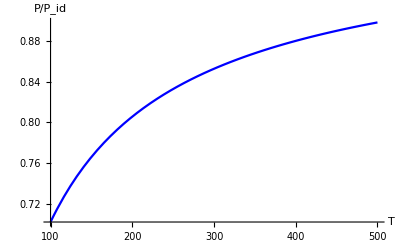

```mathematica
p1=Plot[Re[Pgw1n[T,176]],{T,100,500},PlotStyle->Blue,AxesLabel->{"T","P/P_id"},PlotRange->All]
```

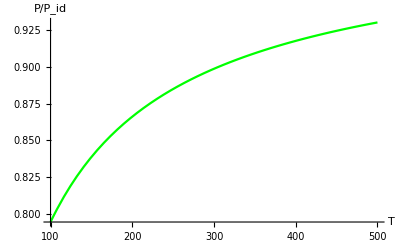

```mathematica
p5=Plot[Re[Pgw1n[T,176]],{T,100,500},PlotStyle->Green,AxesLabel->{"T","P/P_id"},PlotRange->All]
```

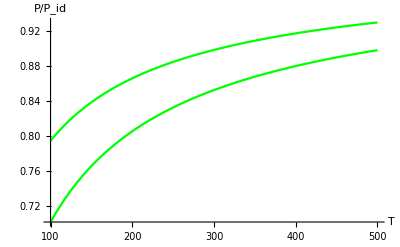

```mathematica
Show[p1,p5]
```

```mathematica
p3=Plot[Re[Pgw1n[T,176]],{T,100,500},PlotStyle->Blue,AxesLabel->{"T","P/P_id"}]
```

-Graphics-

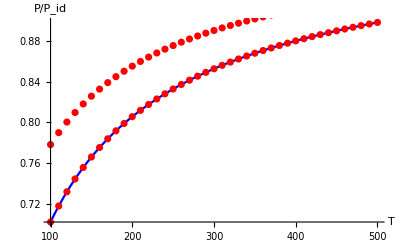

```mathematica
Show[%,p3,p2]
```

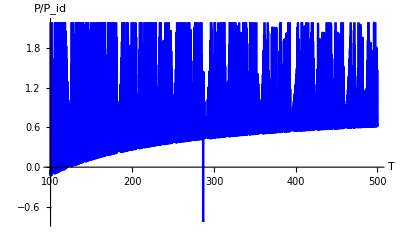

```mathematica
Plot[Re[Pgw1n[T,176]],{T,100,500},PlotStyle->Blue,AxesLabel->{"T","P/P_id"}]
```

```mathematica
xx=Table[Evaluate[Re[Pgw1n[T,176]]],{T,100,500,10}]
```

{0.7021,0.71783,0.731844,0.744405,0.755727,0.765985,0.775327,0.78387,0.791717,0.798951,0.805644,0.811855,0.817636,0.823033,0.828083,0.832821,0.837274,0.84147,0.84543,0.849175,0.852722,0.856087,0.859284,0.862327,0.865226,0.867991,0.870633,0.873159,0.875578,0.877895,0.880119,0.882253,0.884305,0.886279,0.888179,0.89001,0.891775,0.893478,0.895122,0.896711,0.898248}

```mathematica
xy=Table[100+10x,{x,0,40}]
```

{100,110,120,130,140,150,160,170,180,190,200,210,220,230,240,250,260,270,280,290,300,310,320,330,340,350,360,370,380,390,400,410,420,430,440,450,460,470,480,490,500}

```mathematica
xyz=Table[{xy[[i]],xx[[i]]},{i,1,41}]
```

{{100,0.7021},{110,0.71783},{120,0.731844},{130,0.744405},{140,0.755727},{150,0.765985},{160,0.775327},{170,0.78387},{180,0.791717},{190,0.798951},{200,0.805644},{210,0.811855},{220,0.817636},{230,0.823033},{240,0.828083},{250,0.832821},{260,0.837274},{270,0.84147},{280,0.84543},{290,0.849175},{300,0.852722},{310,0.856087},{320,0.859284},{330,0.862327},{340,0.865226},{350,0.867991},{360,0.870633},{370,0.873159},{380,0.875578},{390,0.877895},{400,0.880119},{410,0.882253},{420,0.884305},{430,0.886279},{440,0.888179},{450,0.89001},{460,0.891775},{470,0.893478},{480,0.895122},{490,0.896711},{500,0.898248}}

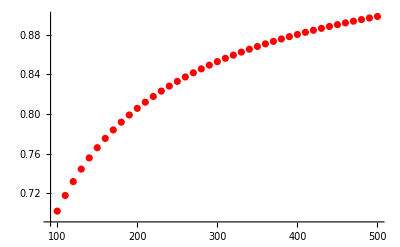

```mathematica
p4=ListPlot[xyz,PlotStyle->Red]
```

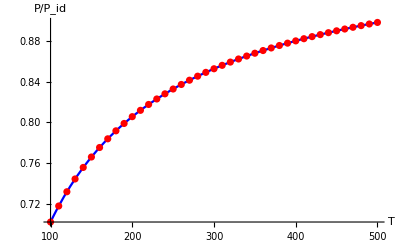

```mathematica
Show[p3,p4]
```

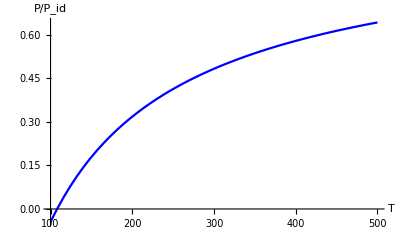

```mathematica
p2=Plot[Pgw1n[T,176],{T,100,500},PlotStyle->Blue,AxesLabel->{"T","P/P_id"}]
```

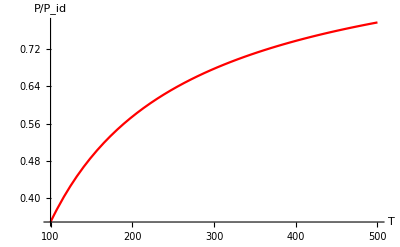

```mathematica
p1=Plot[Pgw1n[T,176],{T,100,500},PlotStyle->Red,AxesLabel->{"T","P/P_id"}]
```

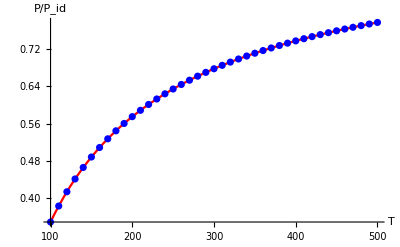

```mathematica
Show[p1,p3]
```

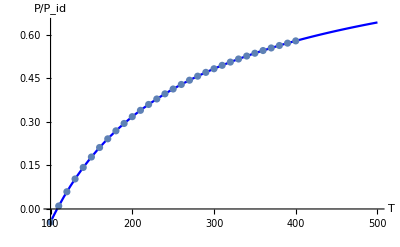

```mathematica
Show[p2,p3]
```

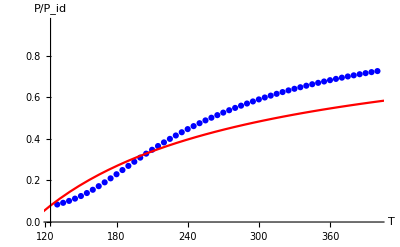

```mathematica
Show[plattice,p1]
```

```mathematica
(*Pcompplots for diff A+*)
```

```mathematica
p1=Plot[Pgw1n[T,176],{T,100,500},PlotStyle->Blue,AxesLabel->{"T","P/P_id"}]
```

-Graphics-

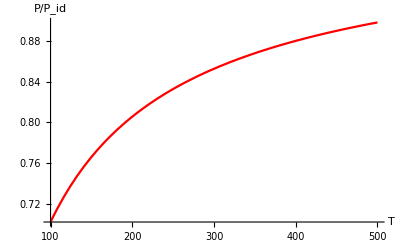

```mathematica
p2=Plot[Pgw1n[T,176],{T,100,500},PlotStyle->Red,AxesLabel->{"T","P/P_id"}]
```

```mathematica
Pideal[100]//N
```

2.19325×10^8

```mathematica
Pgw1[100,176]//N
```

2.26069×10^8

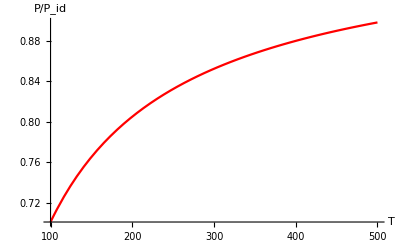

```mathematica
p2=Plot[Pgw1n[T,176],{T,100,500},PlotStyle->Red,AxesLabel->{"T","P/P_id"}]
```

```mathematica
Table[{T,Pgw1n[T,176]},{T,100,500,10}]
```

{{100,0.7021},{110,0.71783},{120,0.731844},{130,0.744405},{140,0.755727},{150,0.765985},{160,0.775327},{170,0.78387},{180,0.791717},{190,0.798951},{200,0.805644},{210,0.811855},{220,0.817636},{230,0.823033},{240,0.828083},{250,0.832821},{260,0.837274},{270,0.84147},{280,0.84543},{290,0.849175},{300,0.852722},{310,0.856087},{320,0.859284},{330,0.862327},{340,0.865226},{350,0.867991},{360,0.870633},{370,0.873159},{380,0.875578},{390,0.877895},{400,0.880119},{410,0.882253},{420,0.884305},{430,0.886279},{440,0.888179},{450,0.89001},{460,0.891775},{470,0.893478},{480,0.895122},{490,0.896711},{500,0.898248}}

```mathematica
p2=ListPlot[%,PlotStyle->Red]
```

-Graphics-

```mathematica
(*A+=0.0001,0.01,1.1,c2=0*)
```

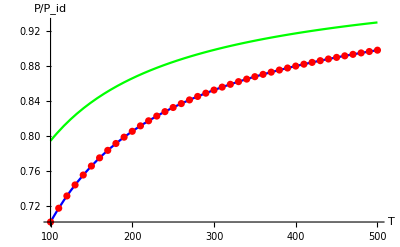

```mathematica
Show[p1,p2,p5]
```

```mathematica
(*all individual plots*)
```

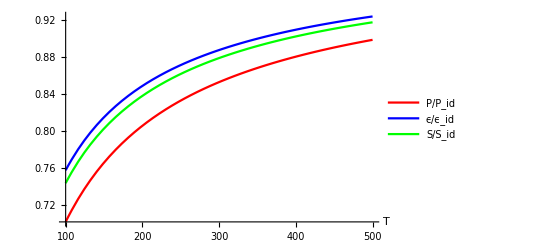

```mathematica
Plot[{Re[Pgw1n[T,176]],Re[Endengw1n[T,176]],Re[Sdengw1n[T,176]]},{T,100,500},AxesLabel->{"T"},PlotStyle->{Red,Blue,Green},PlotLegends->Placed[{"P/P_id","ϵ/ϵ_id","S/S_id"},{Right,Center}]]
```

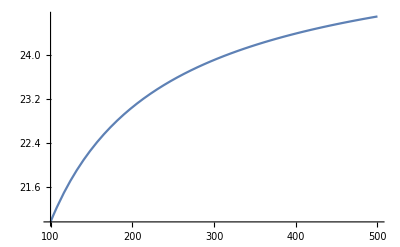

```mathematica
Plot[Spheatgw1n[T,176],{T,100,500}]
```

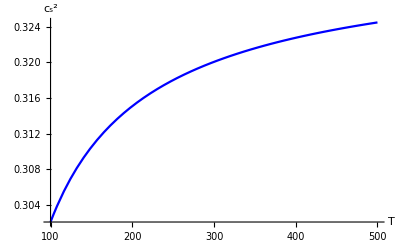

```mathematica
Plot[Soundspdgw[T,100],{T,100,500},AxesLabel->{"T","c_s^2"},PlotStyle->{Blue}]
```

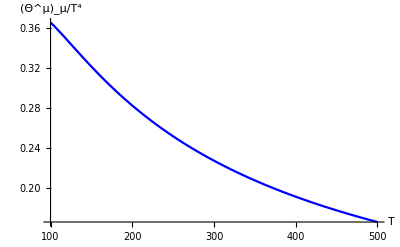

```mathematica
Plot[Conanamoly1[T,176],{T,100,500},AxesLabel->{"T","(Θ^μ)_μ/T^4"},PlotStyle->{Blue}]
```

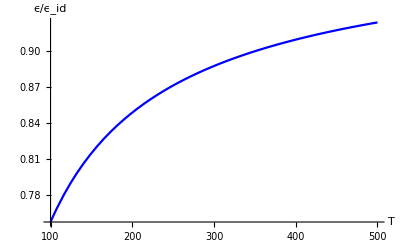

```mathematica
Plot[Re[Endengw1n[T,176]],{T,100,500},AxesLabel->{"T","ϵ/ϵ_id"},PlotStyle->Blue]
```

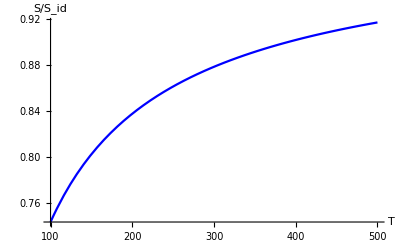

```mathematica
Plot[Re[Sdengw1n[T,176]],{T,100,500},AxesLabel->{"T","S/S_id"},PlotStyle->Blue]
```

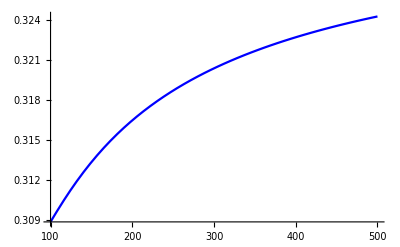

```mathematica
Plot[Re[Pgw1[T,176]]/Re[Endengw1[T,176]],{T,100,500},PlotStyle->Blue]
```

## Others:

## Special functions expansions at zero

```mathematica
2 EllipticK[2]//N
```

2.62206-2.62206 ⅈ

```mathematica
Gamma[1]
```

1

```mathematica
Zeta[3]//N
```

1.20206

```mathematica
Series[Zeta[2x+3],{x,0,1}]
```

Zeta[3]+2 Zeta'[3] x+O[x]^2

```mathematica
Series[Gamma[x+3/2],{x,0,1}]
```

(√π)/2+1/2 √π PolyGamma[0,3/2] x+O[x]^2

```mathematica
Series[Gamma[x+5/2],{x,0,1}]
```

(3 √π)/4+3/4 √π PolyGamma[0,5/2] x+O[x]^2

```mathematica
(√π)/2+1/2 √π PolyGamma[0,3/2] x-4/3((15 √π)/8-15/8 √π PolyGamma[0,7/2] x)//Simplify
```

1/2 √π (-4+x (PolyGamma[0,3/2]+5 PolyGamma[0,7/2]))

```mathematica
(√π)/2+1/2 √π PolyGamma[0,3/2] x-2((3 √π)/4+3/4 √π PolyGamma[0,5/2] x)//Simplify
```

1/2 √π (-2+x (PolyGamma[0,3/2]-3 PolyGamma[0,5/2]))

```mathematica
PolyGamma[1/2]//N
```

-1.96351

```mathematica
(PolyGamma[1/2]-PolyGamma[3/2])//N
```

-2.

```mathematica
Series[Gamma[x+1],{x,0,1}]
```

1-EulerGamma x+O[x]^2

```mathematica
Series[Gamma[1/2+z/2],{z,0,1}]
```

√π+1/2 √π PolyGamma[0,1/2] z+O[z]^2

```mathematica
PolyGamma[0,-3/2]//N
```

0.703157

```mathematica
Series[HurwitzZeta[2x-3,1/2+y],{x,0,1}]
```

HurwitzZeta[-3,1/2+y]+2 HurwitzZeta^(1,0)[-3,1/2+y] x+O[x]^2

```mathematica
Series[Zeta[2x+1],{x,0,1}]
```

1/(2 x)+EulerGamma-2 StieltjesGamma[1] x+O[x]^2

```mathematica
Series[HurwitzZeta[2x+1,1/2],{x,0,1}]
```

1/(2 x)+(EulerGamma+2 Log[2])+(4 EulerGamma Log[2]+2 Log[2]^2-2 StieltjesGamma[1]) x+O[x]^2

```mathematica
BernoulliB[4,(1/2+x)]//Expand//Simplify
```

7/240-x^2/2+x^4

```mathematica
%21+1/30
```

1/16-x^2/2+x^4

```mathematica
-1/30+1/16
```

7/240

```mathematica
Integrate[t^(-1+x) Exp[-y/t],{t,0,Infinity}]
```

ConditionalExpression[y^x Gamma[-x], Re[x]<0&&((Re[y]==0&&1+Re[x]>0)||Re[y]>0)]

```mathematica
Integrate[p^2 Log[1-Exp[-b p]],{p,0,Infinity}]
```

ConditionalExpression[-π^4/(45 b^3), Re[b]>0]

```mathematica
Clear[m]
```

```mathematica
M={{-I ω +μ-m,0,-p3,-p1+I p2},{0,-I ω+μ-m,-p1-I p2,p3},{-p3,-p1+I p2,-I ω+μ+m,0},{-p1-I p2,p3,0,-I ω+μ+m}}
```

{{-m+μ-ⅈ ω,0,-p3,-p1+ⅈ p2},{0,-m+μ-ⅈ ω,-p1-ⅈ p2,p3},{-p3,-p1+ⅈ p2,m+μ-ⅈ ω,0},{-p1-ⅈ p2,p3,0,m+μ-ⅈ ω}}

```mathematica
Det[M]
```

m^4+2 m^2 p1^2+p1^4+2 m^2 p2^2+2 p1^2 p2^2+p2^4+2 m^2 p3^2+2 p1^2 p3^2+2 p2^2 p3^2+p3^4-2 m^2 μ^2-2 p1^2 μ^2-2 p2^2 μ^2-2 p3^2 μ^2+μ^4+4 ⅈ m^2 μ ω+4 ⅈ p1^2 μ ω+4 ⅈ p2^2 μ ω+4 ⅈ p3^2 μ ω-4 ⅈ μ^3 ω+2 m^2 ω^2+2 p1^2 ω^2+2 p2^2 ω^2+2 p3^2 ω^2-6 μ^2 ω^2+4 ⅈ μ ω^3+ω^4

```mathematica
Simplify[%17]
```

(m^2+p1^2+p2^2+p3^2-μ^2+2 ⅈ μ ω+ω^2)^2

```mathematica
2 EllipticK[2]//N
```

2.62206-2.62206 ⅈ

```mathematica
JacobiSN[-I+2 I EllipticK[2] ,-1]//N
```

0.-0.907683 ⅈ

```mathematica
JacobiSN[4 EllipticK[-1],-1]
```

0

```mathematica
Integrate[JacobiSN[t,-1],{t,0,4 EllipticK[-1]}]
```

0

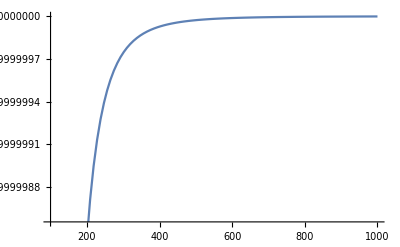

```mathematica
Plot[1-(6*15*4π*12π)/(4 *π^2 22 T^4 Log[(2π T)/176])+(11*6*15)/(16*3*π^4 T^4)Log[(2π T)/(4π T)],{T,100,1000}]
```

```mathematica
a=0.5;
```

```mathematica
Plot3D[{X Sinh[a T],X Cosh[a T]},{X,-10,10},{T,-10,10}]
```

-Graphics3D-

## For third coefficient of HK expansion:

```mathematica
Clear[t]
```

```mathematica
coord={t,x,y,z};
n=4;(*# of spacetime dimensions*)
```

```mathematica
(*Euclidean*)
```

```mathematica
gdd={{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}};
gUU= {{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}};
```

```mathematica
(*Christoffel  symbols*)
```

```mathematica
ΓUdd=Table[1/2 Sum[gUU[[i]][[l]](D[gdd[[l]][[k]],coord[[j]]]+D[gdd[[l]][[j]],coord[[k]]]-D[ gdd[[j]][[k]],coord[[l]]]),{l,1,n}],{i,1,n},{j,1,n},{k,1,n}];
```

```mathematica
Fadd1={{0,I D[U[-I t],t],0,0},{-I D[U[-I t],t],0,0,0},{0,0,0,U[-I t]^2},{0,0,-U[-I t]^2,0}}
```

{{0,U'[-ⅈ t],0,0},{-U'[-ⅈ t],0,0,0},{0,0,0,U[-ⅈ t]^2},{0,0,-U[-ⅈ t]^2,0}}

```mathematica
%//MatrixForm
```

(0 | U'[-ⅈ t] | 0 | 0
-U'[-ⅈ t] | 0 | 0 | 0
0 | 0 | 0 | U[-ⅈ t]^2
0 | 0 | -U[-ⅈ t]^2 | 0)

```mathematica
Fadd2={{0,0,I D[U[t],t],0},{0,0,0,-U[t]^2},{-I D[U[t],t],0,0,0},{0,U[t]^2,0,0}}
```

{{0,0,ⅈ U'[t],0},{0,0,0,-U[t]^2},{-ⅈ U'[t],0,0,0},{0,U[t]^2,0,0}}

```mathematica
Fadd3={{0,0,0,I D[U[t],t]},{0,0,U[t]^2,0},{0,-U[t]^2,0,0},{-I D[U[t],t],0,0,0}}
```

{{0,0,0,ⅈ U'[t]},{0,0,U[t]^2,0},{0,-U[t]^2,0,0},{-ⅈ U'[t],0,0,0}}

```mathematica
Fadd={Fadd1,Fadd2,Fadd3}
```

{{{0,ⅈ U'[t],0,0},{-ⅈ U'[t],0,0,0},{0,0,0,U[t]^2},{0,0,-U[t]^2,0}},{{0,0,ⅈ U'[t],0},{0,0,0,-U[t]^2},{-ⅈ U'[t],0,0,0},{0,U[t]^2,0,0}},{{0,0,0,ⅈ U'[t]},{0,0,U[t]^2,0},{0,-U[t]^2,0,0},{-ⅈ U'[t],0,0,0}}}

```mathematica
Fadd[[1]]//MatrixForm
```

(0 | ⅈ U'[t] | 0 | 0
-ⅈ U'[t] | 0 | 0 | 0
0 | 0 | 0 | U[t]^2
0 | 0 | -U[t]^2 | 0)

```mathematica
(*Def F in adjoint rep*)
```

```mathematica
Fadj=Table[Sum[I LeviCivitaTensor[3][[a,c,b]]Fadd[[c]][[i]][[j]],{c,1,3}],{a,1,3},{b,1,3},{i,1,n},{j,1,n}];
```

```mathematica
Sum[Fadj[[a]][[b]][[μ]][[ν]]Fadj[[b]][[c]][[ν]][[λ]]Fadj[[c]][[a]][[λ]][[μ]],{a,1,3},{b,1,3},{c,1,3},{μ,1,n},{ν,1,n},{λ,1,n}]
```

6 ⅈ U[t]^6-18 ⅈ U[t]^2 U'[t]^2

```mathematica
(*Def Covariant derivative in Adjoint rep *)
```

```mathematica
CovDadj=Table[Sum[I LeviCivitaTensor[3][[a,e,b]]D[Fadd[[e]][[μ]][[ν]],coord[λ]],{e,1,3}],{a,1,3},{b,1,3},{μ,1,n},{ν,1,n},{λ,1,n}]-Table[Sum[ LeviCivitaTensor[3][[a,d,c]]LeviCivitaTensor[3][[c,e,b]]Fadd[[e]][[μ]][[ν]],{e,1,3}],{a,1,3},{b,1,3},{μ,1,n},{ν,1,n},{λ,1,n}]
```

## Rough

```mathematica
Integrate[Exp[I k x Exp[α T]] x^(I k1/α)Sin[Log[x] k1/α]Exp[I k1 T],T,x]
```

∫(ⅇ^(ⅈ k1 T-T α) (ⅇ^(ⅈ ⅇ^(T α) k x)-x^((2 ⅈ k1)/α) (-ⅈ ⅇ^(T α) k x)^(-(2 ⅈ k1)/α) Gamma[1+(2 ⅈ k1)/α,-ⅈ ⅇ^(T α) k x]))/(2 k)ⅆT

```mathematica
Integrate[(ⅇ^(-T α) (ⅇ^(ⅈ ⅇ^(T α) k x)-x^((2 ⅈ k1)/α) (-ⅈ ⅇ^(T α) k x)^(-(2 ⅈ k1)/α) Gamma[1+(2 ⅈ k1)/α,-ⅈ ⅇ^(T α) k x]))/(2 k)Exp[I k1 T],T]
```

∫(ⅇ^(ⅈ k1 T-T α) (ⅇ^(ⅈ ⅇ^(T α) k x)-x^((2 ⅈ k1)/α) (-ⅈ ⅇ^(T α) k x)^(-(2 ⅈ k1)/α) Gamma[1+(2 ⅈ k1)/α,-ⅈ ⅇ^(T α) k x]))/(2 k)ⅆT